```mathematica
With[{n=4},Table[2^(i-1)x^i,{i,1,n}]]
```

{x,2 x^2,4 x^3,8 x^4}

```mathematica
Total@{x,2 x^2,4 x^3,8 x^4}
```

x+2 x^2+4 x^3+8 x^4

```mathematica
FullSimplify[Normalize@{x,x+2 x^2+4 x^3+8 x^4}.{1,0},x∈Reals]
```

x/(√(x^2+(x+2 x^2+4 x^3+8 x^4)^2))

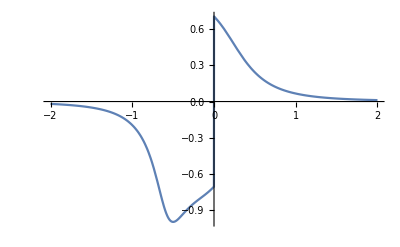

```mathematica
Plot[x/(√(x^2+(x+2 x^2+4 x^3+8 x^4)^2)),{x,-2,2}]
```

```mathematica
FullSimplify[Abs[Normalize@{x,x+2 x^2+4 x^3+8 x^4}.{1,0}],x∈Reals]
```

Abs[x]/(√(x^2+(x+2 x^2+4 x^3+8 x^4)^2))

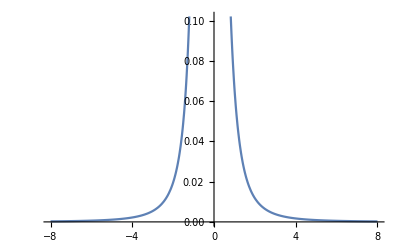

```mathematica
Plot[Abs[x]/(√(x^2+(x+2 x^2+4 x^3+8 x^4)^2)),{x,-8,8}]
```

```mathematica
Manipulate[
NIntegrate[Abs[x]/(√(x^2+(x+2 x^2+4 x^3+8 x^4)^2)),{x,-a,a}],{a,1,1000000,100000}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-1.48904}. NIntegrate obtained 0.798051 and 0.000793474 for the integral and error estimates.

```mathematica
D[x+2 x^2+4 x^3+8 x^4,{x,2}]==D[x+2 x^2+4 x^3+8 x^4,{x,1}]
```

4+24 x+96 x^2==1+4 x+12 x^2+32 x^3

```mathematica
Reduce[4+24 x+96 x^2==1+4 x+12 x^2+32 x^3]
```

x==Root2.86Root[-3-20 #1-84 #1^2+32 #1^3&,1]2.855383329848099||x==Root-0.115-0.140 ⅈRoot[-3-20 #1-84 #1^2+32 #1^3&,2]-0.11519166492404932||x==Root-0.115+0.140 ⅈRoot[-3-20 #1-84 #1^2+32 #1^3&,3]-0.11519166492404932

```mathematica
Solve[4+24 x+96 x^2==1+4 x+12 x^2+32 x^3,x,Reals]
```

{{x→Root2.86Root[-3-20 #1-84 #1^2+32 #1^3&,1]2.855383329848099}}

```mathematica
x+2 x^2+4 x^3+8 x^4
```

x+2 x^2+4 x^3+8 x^4

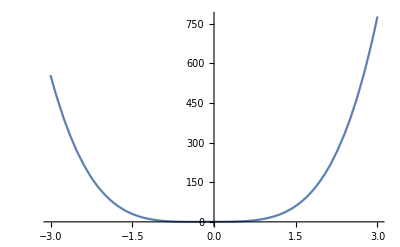

```mathematica
Plot[x+2 x^2+4 x^3+8 x^4,{x,-3.,3.}]
```

```mathematica
Series[Sin[x],{n,1,10}]
```

Sin[x]

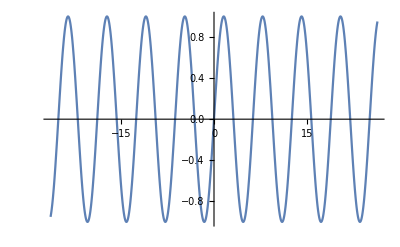

```mathematica
Plot[Sin[x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
Series[Sin[n],{n,1,10}]
```

Sin[1]+Cos[1] (n-1)-1/2 Sin[1] (n-1)^2-1/6 Cos[1] (n-1)^3+1/24 Sin[1] (n-1)^4+1/120 Cos[1] (n-1)^5-1/720 Sin[1] (n-1)^6-(Cos[1] (n-1)^7)/5040+(Sin[1] (n-1)^8)/40320+(Cos[1] (n-1)^9)/362880-(Sin[1] (n-1)^10)/3628800+O[n-1]^11

```mathematica
Series[Sin[n],{n,0,10}]
```

n-n^3/6+n^5/120-n^7/5040+n^9/362880+O[n]^11

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
PadeApproximant[Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11],{x,0,5}]
```

(x-(53 x^3)/396+(551 x^5)/166320)/(1+(13 x^2)/396+(5 x^4)/11088)

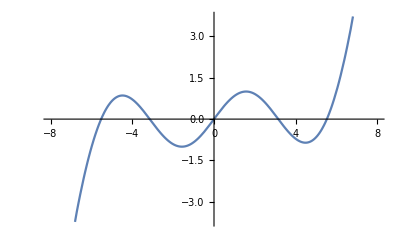

```mathematica
Plot[(x-(53 x^3)/396+(551 x^5)/166320)/(1+(13 x^2)/396+(5 x^4)/11088),{x,-8,8}]
```

```mathematica
InverseSeries[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152+O[x]^11

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

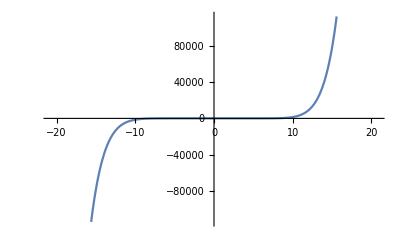

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040+x^9/362880,{x,-20.784609690826528,20.784609690826528}]
```

```mathematica
CoefficientList[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11,x]
```

{0,1,0,-1/6,0,1/120,0,-1/5040,0,1/362880}

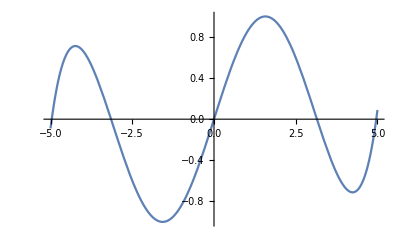

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040+x^9/362880,{x,-5,5}]
```

```mathematica
FullSimplify[Normalize@{x,x-x^3/6+x^5/120-x^7/5040+x^9/362880}.{1,0},x∈Reals]
```

x/(√(x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2))

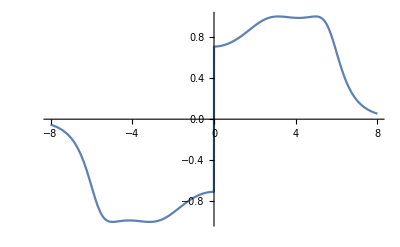

```mathematica
Plot[x/(√(x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2)),{x,-8,8}]
```

```mathematica
(x-x^3/6+x^5/120-x^7/5040+x^9/362880)/x
```

(x-x^3/6+x^5/120-x^7/5040+x^9/362880)/x

```mathematica
FullSimplify[(x-x^3/6+x^5/120-x^7/5040+x^9/362880)/x]
```

1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880

```mathematica
1-x^2/6+x^4/120-x^6/5040+x^8/362880
```

1-x^2/6+x^4/120-x^6/5040+x^8/362880

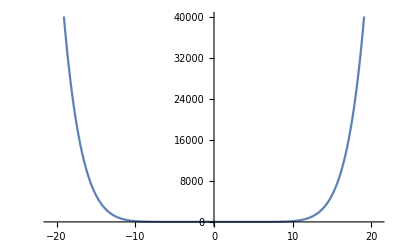

```mathematica
Plot[1-x^2/6+x^4/120-x^6/5040+x^8/362880,{x,-20.784609690826528,20.784609690826528}]
```

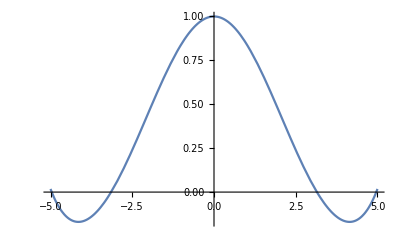

```mathematica
Plot[1-x^2/6+x^4/120-x^6/5040+x^8/362880,{x,-5,5}]
```

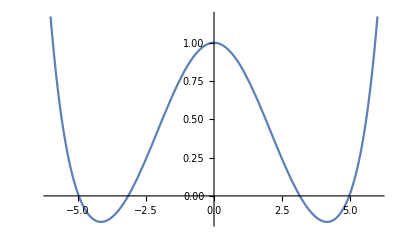

```mathematica
Plot[1-x^2/6+x^4/120-x^6/5040+x^8/362880,{x,-6,6}]
```

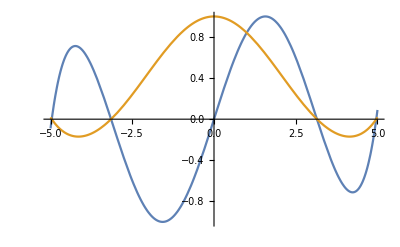

```mathematica
Plot[
{x-x^3/6+x^5/120-x^7/5040+x^9/362880,1-x^2/6+x^4/120-x^6/5040+x^8/362880}
,{x,-5,5}]
```

```mathematica
Normalize@{x,1-x^2/6+x^4/120-x^6/5040+x^8/362880}.{1,0}
```

x/(√(Abs[x]^2+Abs[1-x^2/6+x^4/120-x^6/5040+x^8/362880]^2))

```mathematica
FullSimplify[Normalize@{x,1-x^2/6+x^4/120-x^6/5040+x^8/362880}.{1,0},x∈Reals]
```

x/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2))

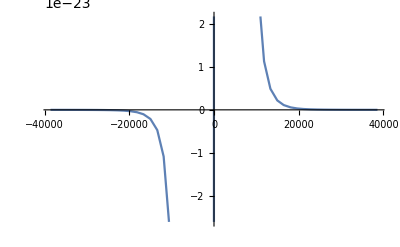

```mathematica
Plot[x/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2)),{x,-38581.270001671815,38581.270001671815}]
```

```mathematica
FullSimplify[Abs[Normalize@{x,1-x^2/6+x^4/120-x^6/5040+x^8/362880}.{1,0}],x∈Reals]
```

Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2))

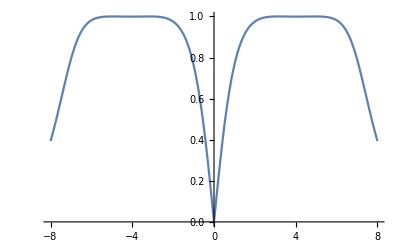

```mathematica
Plot[Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2)),{x,-8,8}]
```

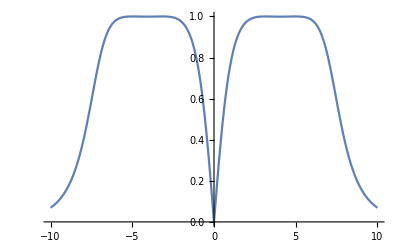

```mathematica
Plot[Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2)),{x,-10,10}]
```

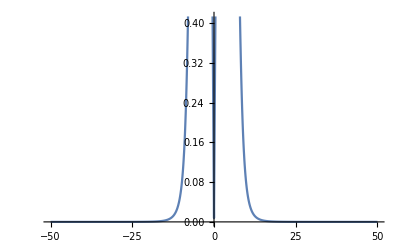

```mathematica
Plot[Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2)),{x,-50,50}]
```

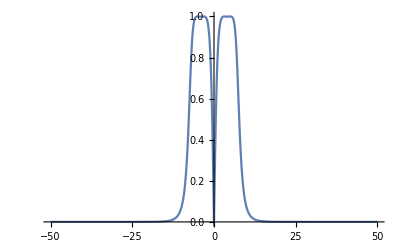

```mathematica
Plot[Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2)),{x,-50,50},PlotRange->Full]
```

```mathematica
NIntegrate[Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2)),{x,-20,20}]
```

14.5839

```mathematica
NIntegrate[Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2)),{x,-20,20}]/40
```

0.364598

```mathematica
NIntegrate[Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2)),{x,-20,20}]/4
```

3.64598

```mathematica
NIntegrate[Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2)),{x,-50,50}]
```

14.5861

```mathematica
Solve[D[Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2)),x]==0,x,Reals]
```

{{x→ConditionalExpression[0,Abs'[0]∈ℝ]},{x→ConditionalExpression[Root-4.96Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,1]-4.963152867179417,Abs'[Root-4.96Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,1]-4.963152867179417]∈ℝ]},{x→ConditionalExpression[Root-3.15Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,2]-3.148690071466962,Abs'[Root-3.15Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,2]-3.148690071466962]∈ℝ]},{x→ConditionalExpression[Root3.15Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,3]3.148690071466962,Abs'[Root3.15Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,3]3.148690071466962]∈ℝ]},{x→ConditionalExpression[Root4.96Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,4]4.963152867179417,Abs'[Root4.96Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,4]4.963152867179417]∈ℝ]},{x→ConditionalExpression[Root-4.04Root[-362880-60480 #1^2+9072 #1^4-360 #1^6+7 #1^8&,1]-4.043175630690929,Abs'[Root-4.04Root[-362880-60480 #1^2+9072 #1^4-360 #1^6+7 #1^8&,1]-4.043175630690929]∈ℝ]},{x→ConditionalExpression[Root4.04Root[-362880-60480 #1^2+9072 #1^4-360 #1^6+7 #1^8&,2]4.043175630690929,Abs'[Root4.04Root[-362880-60480 #1^2+9072 #1^4-360 #1^6+7 #1^8&,2]4.043175630690929]∈ℝ]}}

```mathematica
ϕ==1/(ϕ+ϕ)
```

ϕ==1/(2 ϕ)

```mathematica
Reduce[ϕ==1/(2 ϕ)]
```

ϕ==-1/(√2)||ϕ==1/(√2)

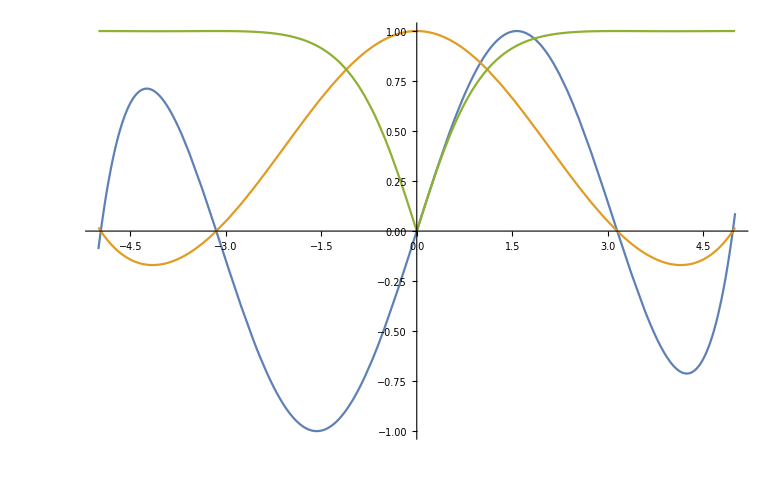

```mathematica
Plot[
{x-x^3/6+x^5/120-x^7/5040+x^9/362880,1-x^2/6+x^4/120-x^6/5040+x^8/362880,Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2))}
,{x,-5,5}]
```

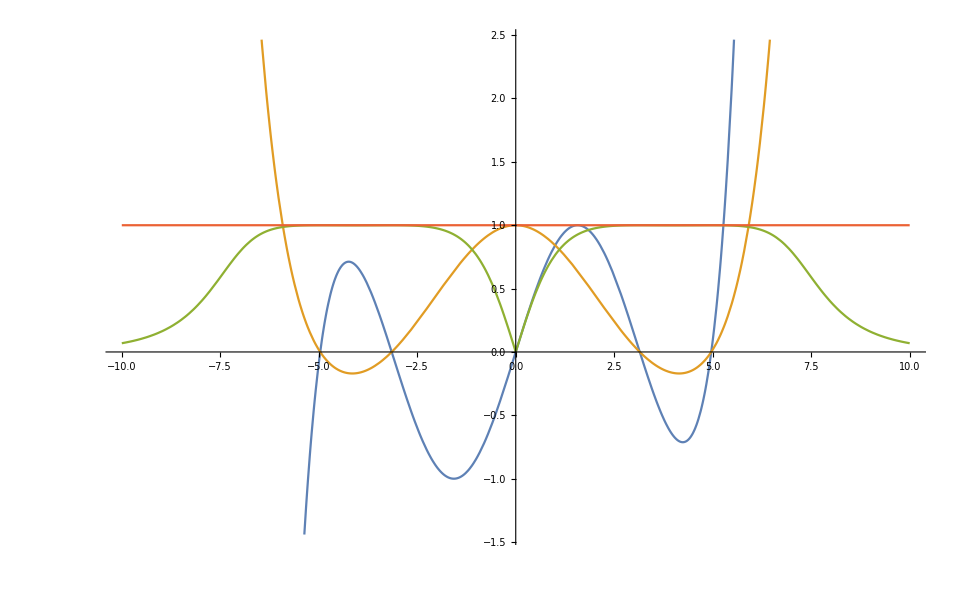

```mathematica
Plot[
{x-x^3/6+x^5/120-x^7/5040+x^9/362880,1-x^2/6+x^4/120-x^6/5040+x^8/362880,Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2)),1}
,{x,-10,10}]
```

```mathematica
Solve[Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2))-1==0,x]
```

{{x→-√(18-1/2 √(-720+1/3 (3668281344-31352832 √13605)^(1/3)+24 2^(2/3) (21 (117+√13605))^(1/3))-1/2 √(-1440-1/3 (3668281344-31352832 √13605)^(1/3)-24 2^(2/3) (21 (117+√13605))^(1/3)+3456/(√(-720+1/3 (3668281344-31352832 √13605)^(1/3)+24 2^(2/3) (21 (117+√13605))^(1/3)))))},{x→√(18-1/2 √(-720+1/3 (3668281344-31352832 √13605)^(1/3)+24 2^(2/3) (21 (117+√13605))^(1/3))-1/2 √(-1440-1/3 (3668281344-31352832 √13605)^(1/3)-24 2^(2/3) (21 (117+√13605))^(1/3)+3456/(√(-720+1/3 (3668281344-31352832 √13605)^(1/3)+24 2^(2/3) (21 (117+√13605))^(1/3)))))},{x→-√(18-1/2 √(-720+1/3 (3668281344-31352832 √13605)^(1/3)+24 2^(2/3) (21 (117+√13605))^(1/3))+1/2 √(-1440-1/3 (3668281344-31352832 √13605)^(1/3)-24 2^(2/3) (21 (117+√13605))^(1/3)+3456/(√(-720+1/3 (3668281344-31352832 √13605)^(1/3)+24 2^(2/3) (21 (117+√13605))^(1/3)))))},{x→√(18-1/2 √(-720+1/3 (3668281344-31352832 √13605)^(1/3)+24 2^(2/3) (21 (117+√13605))^(1/3))+1/2 √(-1440-1/3 (3668281344-31352832 √13605)^(1/3)-24 2^(2/3) (21 (117+√13605))^(1/3)+3456/(√(-720+1/3 (3668281344-31352832 √13605)^(1/3)+24 2^(2/3) (21 (117+√13605))^(1/3)))))}}

```mathematica
Solve[Abs[x]/(√(x^2+(1+(x^2 (-60480+3024 x^2-72 x^4+x^6))/362880)^2))-1==0,x,Reals]
```

{{x→Root-4.96Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,1]-4.963152867179417},{x→Root-3.15Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,2]-3.148690071466962},{x→Root3.15Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,3]3.148690071466962},{x→Root4.96Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,4]4.963152867179417}}

```mathematica
Solve[1-x^2/6+x^4/120-x^6/5040+x^8/362880==0,x,Reals]
```

{{x→Root-4.96Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,1]-4.963152867179417},{x→Root-3.15Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,2]-3.148690071466962},{x→Root3.15Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,3]3.148690071466962},{x→Root4.96Root[362880-60480 #1^2+3024 #1^4-72 #1^6+#1^8&,4]4.963152867179417}}

```mathematica
x^3-x
```

-x+x^3

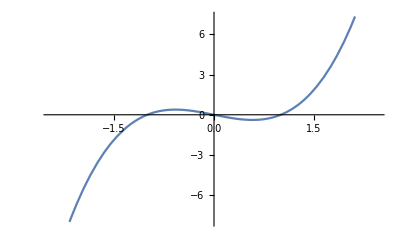

```mathematica
Plot[-x+x^3,{x,-2.449489742783178,2.449489742783178}]
```

```mathematica
FullSimplify[Abs[Normalize@{x,-x+x^3}.{1,0}],x∈Reals]
```

1/(√(2-2 x^2+x^4))

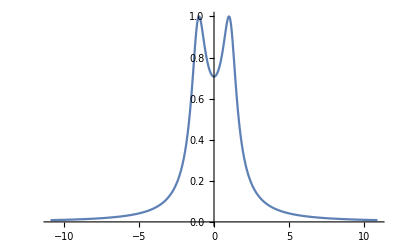

```mathematica
Plot[1/(√(2-2 x^2+x^4)),{x,-10.92,10.92}]
```

```mathematica
(-x+x^3)/x
```

(-x+x^3)/x

```mathematica
Simplify[(-x+x^3)/x]
```

-1+x^2

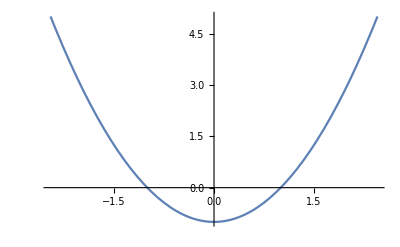

```mathematica
Plot[-1+x^2,{x,-2.449489742783178,2.449489742783178}]
```

```mathematica
FullSimplify[Abs[Normalize@{x,-1+x^2}.{1,0}],x∈Reals]
```

Abs[x]/(√(1-x^2+x^4))

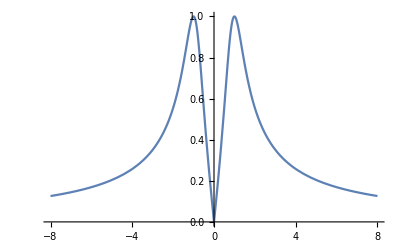

```mathematica
Plot[Abs[x]/(√(1-x^2+x^4)),{x,-8,8}]
```

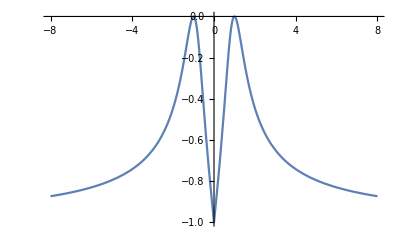

```mathematica
Plot[Abs[x]/(√(1-x^2+x^4))-1,{x,-8,8}]
```

```mathematica
Solve[Abs[x]/(√(1-x^2+x^4))-1,x,Reals]
```

Solve::naqs: -1+Abs[x]/(√(1-x^2+x^4)) is not a quantified system of equations and inequalities.

Solve[-1+Abs[x]/(√(1-x^2+x^4)),x,ℝ]

```mathematica
Solve[Abs[x]/(√(1-x^2+x^4))-1==0,x,Reals]
```

{{x→-1},{x→1}}

```mathematica
{
{Abs[x]/(√(1-x^2+x^4))-1==0},
{Abs[x]/(√(1-x^2+x^4))==1},
{Abs[x]==√(1-x^2+x^4)}
}
```

{{-1+Abs[x]/(√(1-x^2+x^4))==0},{Abs[x]/(√(1-x^2+x^4))==1},{Abs[x]==√(1-x^2+x^4)}}

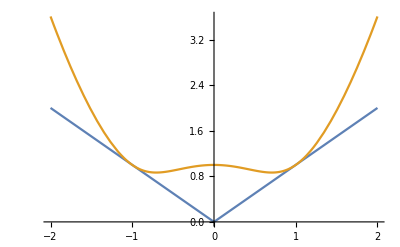

```mathematica
Plot[{Abs[x],√(1-x^2+x^4)},{x,-2,2}]
```

```mathematica
1-x^2+x^4
```

1-x^2+x^4

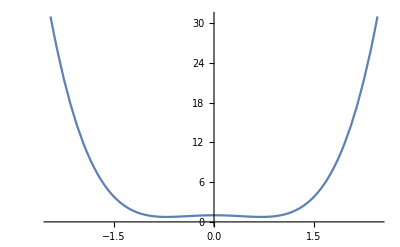

```mathematica
Plot[1-x^2+x^4,{x,-2.449489742783178,2.449489742783178}]
```

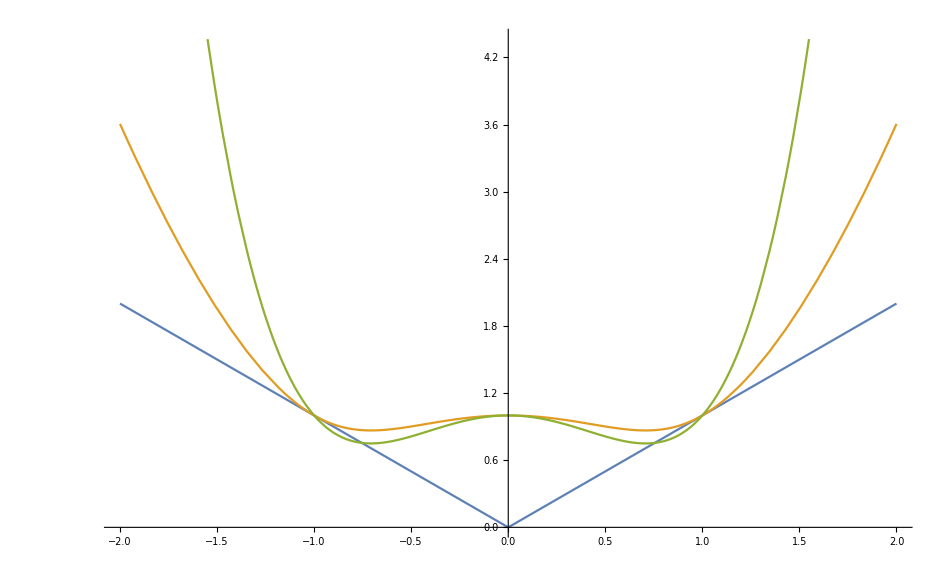

```mathematica
Plot[{Abs[x],√(1-x^2+x^4),1-x^2+x^4},{x,-2,2}]
```

```mathematica
ContourPlot[Abs[x]==√(1-x^2+x^4),{x,-2,2}]
```

ContourPlot::argrx: ContourPlot called with 2 arguments; 3 arguments are expected.

ContourPlot[Abs[x]==√(1-x^2+x^4),{x,-2,2}]

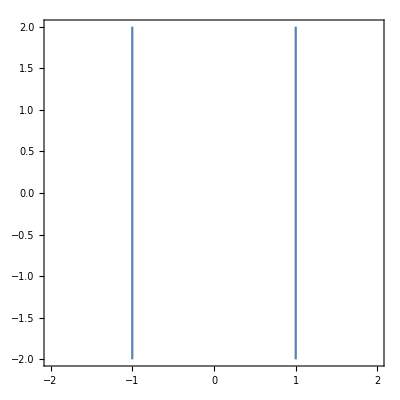

```mathematica
ContourPlot[Abs[x]==√(1-x^2+x^4),{x,-2,2},{y,-2,2}]
```

```mathematica
Manipulate[
Plot[(1-a)x+a(x-1+x^2),{x,-2,2}]
,{a,0,1}]
```

```mathematica
D[(1-a)x+a(x-1+x^2),a]
```

-1+x^2

```mathematica
Plot[-1+x^2,{x,-2.449489742783178,2.449489742783178}]
```

-Graphics-

```mathematica
Manipulate[
Plot[{(1-a)x+a(x-1+x^2),x-1+b x^2},{x,-2,2}]
,{a,0,1},{b,0,1}]
```

Show::gcomb: Could not combine the graphics objects in Show[{,}].

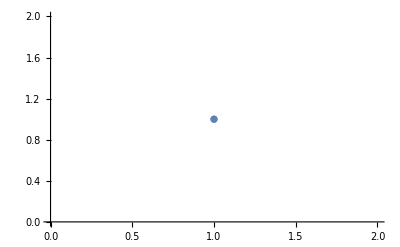
Show[{-Graphics-,}]

```mathematica
Show[{
ListPlot[{{1,1}}],
Manipulate[
Plot[{(1-a)x+a(x-1+x^2),x-1+b x^2},{x,-2,2}]
,{a,0,1},{b,0,1}]
}]
```

```mathematica
Manipulate[
Show[{
ListPlot[{{1,1}}],
Plot[{(1-a)x+a(x-1+x^2),x-1+b x^2},{x,-2,2}]
}],{a,0,1},{b,0,1}
]
```

```mathematica
Manipulate[
Show[{
ListPlot[{{1,1}}],
Plot[{(1-a)x+a(x-1+x^2),x-1+b x^2},{x,-2,2},PlotRange->{{-2,2},{-2,2}}]
}],{a,0,1},{b,0,1}
]
```

```mathematica
ExpandAll[(1-a)x+a(x-1+x^2)]
```

-a+x+a x^2

```mathematica
(((x^3-x)/x-1)/x-1)/x-1
```

-1+(-1+(-1+(-x+x^3)/x)/x)/x

```mathematica
Simplify[-1+(-1+(-1+(-x+x^3)/x)/x)/x]
```

-(2+x)/x^2

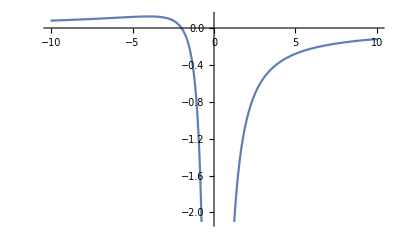

```mathematica
Plot[-(2+x)/x^2,{x,-10.04,10.04}]
```

```mathematica
x x-1
```

-1+x^2

```mathematica
Plot[-1+x^2,{x,-2.449489742783178,2.449489742783178}]
```

-Graphics-

```mathematica
(x^3-x)/x+((x^3-x)/x/.x->0)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
g[x]==f[x]/x
```

g[x]==f[x]/x

```mathematica
g[x]+g[0]
```

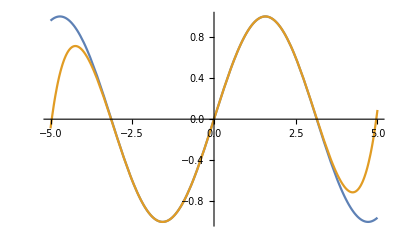

```mathematica
Plot[{Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880},{x,-5,5}]
```

```mathematica
Plot[{Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880},{x,-5,5}]
```

```mathematica
Normalize@{x,Sin[x]}.Normalize@{x,x-x^3/6+x^5/120-x^7/5040+x^9/362880}
```

x^2/(√(Abs[x]^2+Abs[x-x^3/6+x^5/120-x^7/5040+x^9/362880]^2) √(Abs[x]^2+Abs[Sin[x]]^2))+((x-x^3/6+x^5/120-x^7/5040+x^9/362880) Sin[x])/(√(Abs[x]^2+Abs[x-x^3/6+x^5/120-x^7/5040+x^9/362880]^2) √(Abs[x]^2+Abs[Sin[x]]^2))

```mathematica
FullSimplify[Normalize@{x,Sin[x]}.Normalize@{x,x-x^3/6+x^5/120-x^7/5040+x^9/362880},x∈Reals]
```

(x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2)))

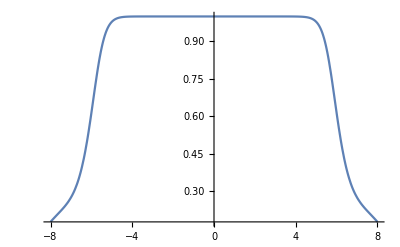

```mathematica
Plot[(x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2))),{x,-8,8}]
```

```mathematica
Solve[(x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2)))==1,x,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(x (362880 x+(362880-60480 x^2+3024 x^4-72 x^6+x^8) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120-x^7/5040+x^9/362880)^2) (x^2+Sin[x]^2)))==1,x,ℝ]

```mathematica
Manipulate[Series[Sin[x],{x,0,a}],{a,1,10,1}]
```

```mathematica
Manipulate[Series[Sin[x],{x,0,a}],{a,1,10,2}]
```

```mathematica
PadeApproximant[Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11],{x,0,5}]
```

(x-(53 x^3)/396+(551 x^5)/166320)/(1+(13 x^2)/396+(5 x^4)/11088)

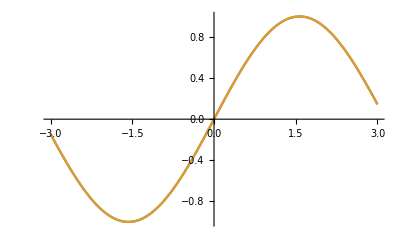

```mathematica
Plot[
{x-x^3/6+x^5/120-x^7/5040+x^9/362880,(x-(53 x^3)/396+(551 x^5)/166320)/(1+(13 x^2)/396+(5 x^4)/11088)}
,{x,-3,3}]
```

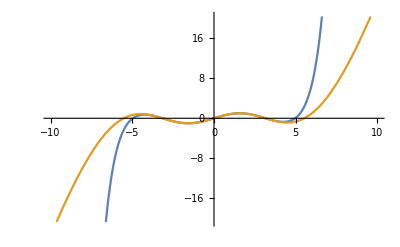

```mathematica
Plot[
{x-x^3/6+x^5/120-x^7/5040+x^9/362880,(x-(53 x^3)/396+(551 x^5)/166320)/(1+(13 x^2)/396+(5 x^4)/11088)}
,{x,-10,10}]
```

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

```mathematica
Manipulate[
With[{sin=Normal@Series[Sin[x],{x,0,a}]},
Plot[{
Sin[x],
sin,
FullSimplify[Abs[Normalize@{x,sin}.{x,Sin[x]}],Element[x,Reals]]
},{x,-5,5}]
],{a,1,10,2}]
```

```mathematica
Manipulate[
With[{sin=Normal@Series[Sin[x],{x,0,a}]},
Plot[{
Sin[x],
sin,
FullSimplify[Abs[Normalize@{x,sin}.{x,Sin[x]}],Element[x,Reals]]
},{x,-10,10}]
],{a,1,10,2}]
```

```mathematica
Manipulate[
With[{sin=Normal@Series[Sin[x],{x,0,a}]},
Plot[{
Sin[x],
sin,
FullSimplify[Abs[Normalize@{x,sin}.Normalize@{x,Sin[x]}],Element[x,Reals]]
},{x,-10,10}]
],{a,1,10,2}]
```

```mathematica
Manipulate[
With[{sin=Normal@Series[Sin[x],{x,0,a}]},
Plot[{
Sin[x],
sin,
FullSimplify[Abs[Normalize@{x,sin}.Normalize@{x,Sin[x]}],Element[x,Reals]]
},{x,-10,10}]
],{a,1,20,2}]
```